Řešení soustav diferenciálních rovnic

Zadnou úlohu převedeme na soustavu N diferenciálních rovnic 1. řádu

úkol 1. Runge-Kuttovou metodou čtvrtého řádu vyřešte Keplerovu úlohu dle tohoto zadání

```mathematica
t=0;(* počáteční čas*)
T=20; (*koncový čas*)
h=.05;(* časový krok*)
(*{u1,u2,u3,u4}={1,-0.3,0,.3};*)(* počáteční podmínky(x,dx/dt,y,dy/dt)*)
{u1,u2,u3,u4}={1,-0.,0,1};
wn={u1,u2,u3,u4}; (*počáteční podmínka se nahraje do proměnné, ve které se bude iterovat řešení*)
listxy={}; (*list pro ukládání polohy*)
energie={}; (*list pro ukládání celkové energie*)
```

```mathematica
f[w_,t_]:={w[[2]],-w[[1]]/(w[[1]]^2+w[[3]]^2)^(3/2),w[[4]],-w[[3]]/(w[[1]]^2+w[[3]]^2)^(3/2)} (* funkce explicitně na čase nezávisí, parametr t je možné vynechat*)
```

```mathematica
While[t<T,
AppendTo[listxy,{wn[[1]],wn[[3]]}];
AppendTo[energie,1/2*(wn[[2]]^2+wn[[4]]^2)-1/Sqrt[wn[[1]]^2+wn[[3]]^2]];(* energie = kinetická + potenciální*)
k1=h*f[wn,h];
k2=h*f[wn+k1/2,t+h/2];
k3=h*f[wn+k2/2,t+h/2];
k4=h*f[wn+k3,t+h];
wn=wn+(k1+2*k2+2*k3+k4)/6;
t=t+h;
]
```

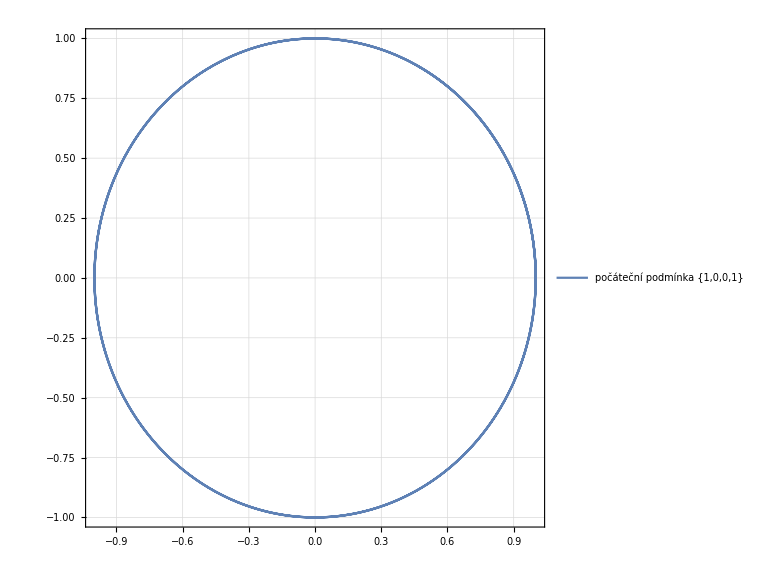

```mathematica
ListPlot[listxy,AspectRatio->Max[listxy[[1]]]/Max[listxy[[2]]],Joined->True,PlotLegends->{"počáteční podmínka {1,0,0,1}","počáteční podmínka {1,-0.3,0,.3}"},ImageSize->Large,Frame->True,FrameStyle->Directive[Gray, 15],GridLines->Automatic]
```